```mathematica
basedir="/home/kamano/gitsrc/ChemicalStructureRecognition"
```

/home/kamano/gitsrc/ChemicalStructureRecognition

```mathematica
SetDirectory[basedir]
```

/home/kamano/gitsrc/ChemicalStructureRecognition

## OSRA check

### Original data

```mathematica
files=FileNames["/home/kamano/gitsrc/ChemicalStructureRecognition/OSRA-test/*"];
```

```mathematica
smilesFile=Cases[files,a_String/;StringMatchQ[a,"*txt"]];
```

```mathematica
IDs=Map[StringReplace[#,{RegularExpression["^.*/OSRA-test/"]->"",".txt"->""}]&,smilesFile]
```

{11401,12604,13235,13509,13838,15290,15397,15657,16301,1661,16933,17023,17242,17538,19707,1989,20008,21714,21734,23711,24766,26901,27756,28281,28913,2945,29820,3040,30646,32027,32286,34262,35978,37166,37508,37832,38012,38397,39628,40439,43288,43691,5184,5540,5810,7405,7486,8595,8924,9910}

```mathematica
smilesStr=Map[Import[#,"String"]&,smilesFile];
```

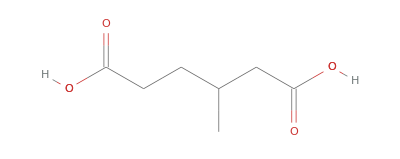

```mathematica
ChemicalData[smilesStr[[1]]]
```

```mathematica
ChemicalData[smilesStr[[1]],"AdjacencyMatrix"]
```

SparseArray[…]

### OSRA Smiles from jpg

```mathematica
jpgSmilesFile=Map[basedir<>"/OSRA-test/"<>#<>".jpg.os"&,IDs];
```

```mathematica
jpgSmiles=Map[Import[#,"String"]&,jpgSmilesFile];
```

### OSRA Smiles from png

```mathematica
ongSmilesFile=Map[basedir<>"/OSRA-test/"<>#<>".png.os"&,IDs];
```

```mathematica
pngSmiles=Map[Import[#,"String"]&,jpgSmilesFile];
```

```mathematica
pngSmiles
```

{OC(=[U])CCC(CC(=N)O)C
,,S=C1CC2C(C1(C)CC2)(C)C
,c1ccc(cc1)Oc1ccccc1
,O=[NH+]c1[nH]c(=O)[nH]c(=O)c1N
,O=C=Nc1ccc(cc1OC)OC
,COc1nc(Cl)nc(n1)Cl
,ClP(C(C)(C)C)C(C)(C)C
,,,,CCCON(OCCC)OCCC
,Sc1cccc(c1)Br
,,[O-][N+](=O)Cc1cccc(c1)S(=O)(=O)N
,CCC(C=C)(F)F
,,Fc1ccccc1C(Cl)(Cl)Cl
,CN(CCC(=O)c1ccccc1)C
,,c1ccc2c(c1)cc1c(c2)sc2c1cccc2
,O=C(C1CCCC=C1)CCCC(=O)c1ccccc1
,,c1[c-]cc(cc1)CN1CCCC1
,,Cc1ccc(cc1)O
,N=C/C(=C(\c1ccccc1)/C1CC=CC=C1)/c1ccccc1
,Cc1cccc(=O)[nH]1
,CCO[C](=CC)(Oc1ccc(cc1)[N+](=O)[O-])OCC
,C*CCC(c1ccccc1)OC1=CC=C(CC1)C(F)(F)F
,,OCC12CCCC(C2C(C23C1CCC(C3)C(=C)C2)C(=O)C)(C)C(=O)[O-]
,,OC1CCC2(C(C1)C(O)CC1C2CCC2(C1CCC2C(CCC(C(C)C)C)C)C)C
,*COC1C(*C(C2CCC=CC2)CN)OC(C(C1O)O)COC1OCC(C(C1O*)O)O
,,CC/C=C/1\C=CC(C=C1)CCCC1CCC(C=C1)C[I+]
,CCC(C(C(C(C(C(C(C(CO)(F)C)(F)C)(F)C)(F)*)(I)C)(F)C)(F)C)(F)*
,CCC1CCCC([C@H]1C)CCC(CCCC(CCCC(CCCC(CCCC(CCCC(C)C)C)C)C)C)C
,CO[C]1(=C)OC2C3C(=CC(=C2c2c(O1)c1c(cc2c2ccccc2)ccc2c1cccc2)c1ccccc1)C=Cc1c3cccc1
,,,,,,IOc1cc(O)c(cc1C)O
,CCCC(CC[I]=N)CC
,O=C1CCCc2c1cccc2
,,}

### memo

```mathematica
StringReplace[smilesFile[[1]],{RegularExpression["^.*/OSRA-test/"]->"",".txt"->""}]
```

11401